# IoT Connectivity and the Wolfram Blockchain

by Tony Koop
Mentor - Matthew Szudzik
with special help from Jesse Friedman

The World Meteorological Organization has over 11,000 weather stations around the world. The data from these devices are continuously recorded into public databases and made available for anyone to download and analyze. Meteorologists regularly inform their viewers with reports produced by Weather, Research & Forecast (WRF) models which analyze these aggregated datasets. In addition to the WMO’s stations, there are also civilian owned weather stations that inform platforms like Weather Underground, AcuRite, and Weather Bug. Unfortunately, those companies do not share the profits they generate off the data they collect from the community and some companies, like AcuRite, no longer offer a public API for their users to easily access their own data. Even worse, WeatherBug has been caught selling private location data about their users to third parties.

Concerns for privacy and data ownership are on the rise. Though Facebook experienced moderate backlash for its role in the Cambridge Analytica scandal, many opine the reaction was insufficient. Switching costs remain high while data produced users remained hosted the platform’s servers.  One way to deal with this is to backup your own data in a secondary location such that it’s available for personal use any time.

Insert your own myAcuRite login credentials into the code below and then evaluate the cell to obtain a table of the latest reading from your personal weather station. After the code retrieves the current data feed, it will be inserted into the Wolfram Blockchain and a public databin which can be accessed at the URL below. If the data is successfully inserted into the blockchain and recalled without changing the data, “True” will appear above the weather table.

 wolfr.am/EM6FHeXi

```mathematica
(*Send a login request with username and password to get a session token and account ID*)
loginData=URLExecute[HTTPRequest[<|
Method->"POST",
"Scheme"->"https",
"Domain"->"marapi.myacurite.com",
"Path"->"/users/login",
"ContentType"->"application/json",
"Body"->ExportString[<|
"email"->"wrfcoin@gmx.com",
"password"->"h5h3f**kD",
"remember"->"True"
|>,"RawJSON"]|>],"RawJSON"];

mytoken=loginData["token_id"];
myaccountid=loginData[["user","account_users",1,"account_id"]];

(*Find the ID of the particular weather station in question*)
hubsData=URLExecute[HTTPRequest[<|
   Method -> "GET",
   "Scheme" -> "https",
   "Domain" -> "marapi.myacurite.com/accounts/"<>ToString[myaccountid]<>"/dashboard/hubs",
   "ContentType"->"application/json",
   "Headers" -> {"x-one-vue-token" -> mytoken}|>],"RawJSON"];
 myhubid=hubsData[["account_hubs",1,"id"]];
 
 (*Otain the current data feed from the particular weather station*)
 weatherfeed=URLExecute[HTTPRequest[<|
   Method -> "GET",
   "Scheme" -> "https",
   "Domain" -> "marapi.myacurite.com/accounts/"<>ToString[myaccountid]<>"/dashboard/hubs/"<>ToString[myhubid],
   "ContentType"->"application/json",
   "Headers" -> {"x-one-vue-token" -> mytoken}|>],"RawJSON"];
   
   (*Organize data. Consider cases with different units*)
   deviceRawData=weatherfeed[["devices",1]];
   sensorRawData=AssociationThread[deviceRawData[["sensors",All,"sensor_name"]]->deviceRawData[["sensors"]]];
   sensorUnits=<|
   "Temperature"->Switch[sensorRawData["Temperature","chart_unit"],"F","DegreesFahrenheit","C","DegreesCelsius"],
   "Pressure"->Switch[sensorRawData["Pressure","chart_unit"],"inHg","InchesOfMercury","hPa","Hectopascals"],
   "Humidity"->"Percent",
   "Wind Speed"->Switch[sensorRawData["Wind Speed","chart_unit"],"mph","Miles"/"Hours","km/h","Kilometers"/"Hours","kn","Knots"],
   "Wind Direction"->"Degrees",
   "Rainfall"->Switch[sensorRawData["Rainfall","chart_unit"],"in","Inches","mm","Millimeters"],
   "Dew Point"->Switch[sensorRawData["Dew Point","chart_unit"],"F","DegreesFahrenheit","C","DegreesCelsius"],
   "Feels Like"->Switch[sensorRawData["Feels Like","chart_unit"],"F","DegreesFahrenheit","C","DegreesCelsius"],
   "Wind Speed Average"->Switch[sensorRawData["Wind Speed","chart_unit"],"mph","Miles"/"Hours","km/h","Kilometers"/"Hours","kn","Knots"]|>;

sensorData=<|"Sensor"->#["sensor_name"],"Value"->Quantity[#["last_reading_value"],sensorUnits[#["sensor_name"]]]|>&/@Values@sensorRawData;

(*Include timestamp, latitude, longitude, and elevation into the table*)
isoStringWithTZToDateObject[string_String]:=
(* by Jesse *)Module[{stringParts=StringSplit[string,RegularExpression["(?=((\\+|-)\\d{2}:\\d{2})|Z$)"]],tzpart,tzoffset,signedtzoffset},Which[Length[stringParts]===1,signedtzoffset=Automatic,ToUpperCase[stringParts[[2]]]==="Z",signedtzoffset=0,True,tzpart=StringSplit[stringParts[[2]],{RegularExpression["(?<=\\+|-)"],":"}];
tzoffset=NumberCompose[FromDigits/@Rest[tzpart],{1,1/60}];
signedtzoffset=N@If[tzpart[[1]]==="-",-tzoffset,tzoffset];];
DateObject[stringParts[[1]],TimeZone->signedtzoffset]]

weatherEntry=dataTable=<|
"Sensors"->sensorData,
"Timestamp"->TimeZoneConvert[isoStringWithTZToDateObject[deviceRawData["last_check_in_at"]]],
"Position"->GeoPosition[Append[
Interpreter["Real"][{weatherfeed["latitude"],weatherfeed["longitude"]}],
Quantity[weatherfeed["elevation"],Switch[weatherfeed["elevation_unit"],"ft","Feet","m","Meters"]]]]|>;

convertWeatherEntryToCompleteSet[weatherEntry_]:= Module[
	{sensorData, time, geolocation, sensorIndex = 1, timeIndex = 2, positionIndex = 3},	
	sensorData = Values /@ Values[weatherEntry]⟦sensorIndex⟧;
	time = "Timestamp" -> Values[weatherEntry]⟦timeIndex⟧;
	geolocation = "Position" -> Values[weatherEntry]⟦positionIndex⟧;	
	Association @ Flatten @ Join[{time, geolocation, Rule @@@ sensorData}]]

(*Insert the weatherEntry and its hash into the Wolfram Blockchain and a Databin*)
weatherHash=Hash[weatherEntry, "SHA256"];
list={weatherHash, weatherEntry};
trxID=BlockchainPut[list];
AppendTo[list, trxID];
DatabinAdd["EM6FHeXi",list];

(*Check that the entry returned from the blockchain computes the same weatherHash, recall last ten entries into Databin*)
Hash[BlockchainGet[trxID]⟦2⟧, "SHA256"]===weatherHash
convertWeatherEntryToCompleteSet[weatherEntry]//Dataset
```

True

Dataset[<>]

# Location Mapping

Data deserts in the field of meteorology exist in places like northern Canada, inland China, and North Africa. A typical Wold Meteorological Organization weather station costs on the order of One of the largest factors contributing to weather forecasting inaccuracy is th    Compare the data feed from the weather station to the nearest World Meteorological Organization station. Could a BenchTable be used to neatly display all entries?

Take 100 random locations across the US and calculate the average “proximity value” for those areas.
Also calculate areas of least density and their proximity value

```mathematica
(*Display a map showing the location of the weather station*)
GeoGraphics[GeoMarker[Interpreter["Real"][{weatherfeed["latitude"],weatherfeed["longitude"]}]
],GeoRange->Quantity[3,"Miles"]]
```

-Graphics-

```mathematica
(*Given the location of WMO stations, find the areas of least density where new stations should be installed*)

(*Import the dataset WMO stations:*)
WMOStations=ResourceObject["WMO Meteorological Stations"];

WMOLocations=Values@ResourceData["WMO Meteorological Stations"][Select[#Country==="United States"&], "Position"];

(*Plot the location of all WMO stations:*)
GeoListPlot[WMOLocations]

(*Visualize the areas with least density*)
```

-Graphics-

```mathematica
(*Given the location of WMO weather stations, calculate radius to cirumscribe 50 WMO stations.
Can we find the location and data of civilian weather stations contributing to AcuRite or WeatherBug??*)
```

```mathematica
{weatherfeed["latitude"],weatherfeed["longitude"]}
```

Values::invrl: The argument {42.387012,-71.220635} is not a valid Association or a list of rules.

Values[{42.387012,-71.220635}]

```mathematica
{"42.387012","-71.220635"}//FullForm
```

List["42.387012","-71.220635"]

```mathematica
loc=GeoPosition[Values@{weatherfeed["latitude"],weatherfeed["longitude"]}]
```

GeoPosition::ltrng: Invalid latitude specification 42.387012.

GeoPosition[{42.387012,-71.220635}]

```mathematica
closest=GeoNearest[Normal[WMOLocations],{42.387012,-71.220635}]
closest2=GeoNearest[Normal[WMOLocations],GeoPosition[{weatherfeed["latitude"],weatherfeed["longitude"]}]]//FullForm
```

```mathematica
ToExpression/@{weatherfeed["latitude"],weatherfeed["longitude"]}//FullForm
```

List[42.387,-71.2206]

```mathematica
(*Find the closest WMO weather station and compare the data from your weather station*)
closest=GeoNearest[Normal[WMOLocations],{42.387012,-71.220635}]

closestfifty=GeoNearest[Normal[WMOLocations], {42.387012,-71.220635}, 50]; (*returns n nearest values*)

Mean[GeoDistanceList[closestfifty]](*take the average of this*)
```

{GeoPosition[{41.8,-71.4667}]}

163.894 mi

```mathematica
(*Find the closest WMO weather station and compare the data from your weather station*)
GeoNearest[WMOStations, {weatherfeed["latitude"],weatherfeed["longitude"]}]

closestfifty=GeoNearest[closest, loc, 50] (*returns n nearest values*)

GeoDistanceList[closestfifty] (*take the average of this*)
```

```mathematica
GeoPosition[{weatherfeed["latitude"],weatherfeed["longitude"]}]
```

GeoPosition::ltrng: Invalid latitude specification 42.387012.

GeoPosition[{42.387012,-71.220635}]

# Data Charting & Visualization

Compare the data feed from the weather station to the nearest World Meteorological Organization station(WMO12345). Could a BenchTable be used to neatly display all entries?

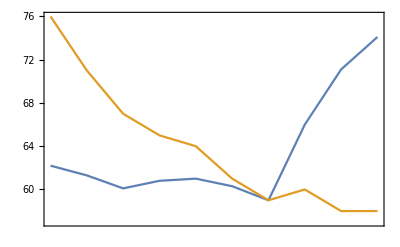

```mathematica
(*Collect all the Blockchain sumbissions from the weather station and chart the temperature over time*)  
Databin["EM6FHeXi", All];
recentHashes=Normal[Dataset[Databin["EM6FHeXi", -10]]][[All,1,-1]];
data=Dataset[BlockchainGet[recentHashes]];
times=data[[1;;All,2,2]]//Normal;
temps=data[[1;;All,2,1,1,2]]//Normal;
myTempsTimeSeries=TimeSeries[Transpose[{times, MapAt[ToExpression,#,1]&/@temps}]];
wmoTempsTimeSeries=TimeSeries[Transpose[{times, AirTemperatureData["KBED", times]}]];
DateListPlot[{myTempsTimeSeries,wmoTempsTimeSeries}]
```

```mathematica
WeatherData["KBED","Humidity",Take[times,3]]
```

WeatherData::notsubprop: {{2019, 7, 8, 0, 16, 7.}, {2019, 7, 8, 1, 16, 7.}, {2019, 7, 8, 2, 16, 6.}} is not a known subproperty of WeatherData. Use subproperty "Properties" for a list of subproperties.

WeatherData[KBED,Humidity,{Mon 8 Jul 2019 00:16:07GMT-4.,Mon 8 Jul 2019 01:16:07GMT-4.,Mon 8 Jul 2019 02:16:06GMT-4.}]

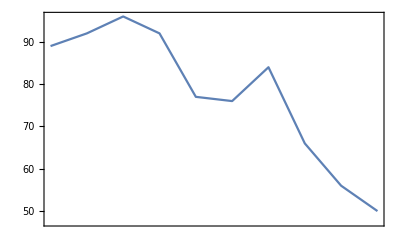

TimeSeries[…]

WeatherData::notsubprop: {{2019, 7, 8, 0, 16, 7.}, {2019, 7, 8, 1, 16, 7.}, {2019, 7, 8, 2, 16, 6.}, {2019, 7, 8, 3, 16, 7.}, {2019, 7, 8, 4, 16, 7.}, {2019, 7, 8, 5, 16, 7.}, {2019, 7, 8, 6, 16, 6.}, {2019, 7, 8, 7, 16, 6.}, {2019, 7, 8, 8, 16, 6.}, {2019, 7, 8, 9, 16, 8.}} is not a known subproperty of WeatherData. Use subproperty "Properties" for a list of subproperties.

Transpose::nmtx: The first two levels of {{DateObject[{2019,7,8,0,16,7.},Instant,Gregorian,-4.],DateObject[{2019,7,8,1,16,7.},Instant,Gregorian,-4.],DateObject[{2019,7,8,2,16,6.},Instant,Gregorian,-4.],DateObject[{2019,7,8,3,16,7.},Instant,Gregorian,-4.],DateObject[{2019,7,8,4,16,7.},Instant,Gregorian,-4.],«1»,DateObject[{2019,7,8,6,16,6.},Instant,Gregorian,-4.],DateObject[{2019,7,8,7,16,6.},Instant,Gregorian,-4.],DateObject[{2019,7,8,8,16,6.},Instant,Gregorian,-4.],DateObject[{2019,7,8,9,16,8.},Instant,Gregorian,-4.]},«1»} cannot be transposed.

DateListPlot::ldata: … is not a valid dataset or list of datasets.

DateListPlot[{TimeSeries[…],TimeSeries[Transpose[{{Mon 8 Jul 2019 00:16:07GMT-4.,Mon 8 Jul 2019 01:16:07GMT-4.,Mon 8 Jul 2019 02:16:06GMT-4.,Mon 8 Jul 2019 03:16:07GMT-4.,Mon 8 Jul 2019 04:16:07GMT-4.,Mon 8 Jul 2019 05:16:07GMT-4.,Mon 8 Jul 2019 06:16:06GMT-4.,Mon 8 Jul 2019 07:16:06GMT-4.,Mon 8 Jul 2019 08:16:06GMT-4.,Mon 8 Jul 2019 09:16:08GMT-4.},WeatherData[KBED,Humidity,{Mon 8 Jul 2019 00:16:07GMT-4.,Mon 8 Jul 2019 01:16:07GMT-4.,Mon 8 Jul 2019 02:16:06GMT-4.,Mon 8 Jul 2019 03:16:07GMT-4.,Mon 8 Jul 2019 04:16:07GMT-4.,Mon 8 Jul 2019 05:16:07GMT-4.,Mon 8 Jul 2019 06:16:06GMT-4.,Mon 8 Jul 2019 07:16:06GMT-4.,Mon 8 Jul 2019 08:16:06GMT-4.,Mon 8 Jul 2019 09:16:08GMT-4.}]}]]}]

```mathematica
(*Chart the weather station's Humidity*)
humidity=data[[1;;All,2,1,2,2]]//Normal;
DateListPlot[Transpose[{times, MapAt[ToExpression,#,1]&/@humidity}]]

myHumidityTimeSeries=TimeSeries[Transpose[{times, MapAt[ToExpression,#,1]&/@humidity}]]
wmoHumidityTimeSeries=TimeSeries[Transpose[{times, WeatherData["KBED", "Humidity", times]}]];
DateListPlot[{myHumidityTimeSeries,wmoHumidityTimeSeries}]
```

```mathematica
times
```

{Mon 8 Jul 2019 00:16:07GMT-4.,Mon 8 Jul 2019 01:16:07GMT-4.,Mon 8 Jul 2019 02:16:06GMT-4.,Mon 8 Jul 2019 03:16:07GMT-4.,Mon 8 Jul 2019 04:16:07GMT-4.,Mon 8 Jul 2019 05:16:07GMT-4.,Mon 8 Jul 2019 06:16:06GMT-4.,Mon 8 Jul 2019 07:16:06GMT-4.,Mon 8 Jul 2019 08:16:06GMT-4.,Mon 8 Jul 2019 09:16:08GMT-4.}

```mathematica
WeatherData["KBED", "Humidity"]
```

0.466

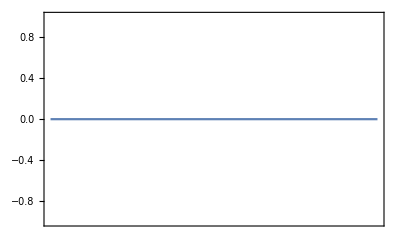

```mathematica
(*Chart the weather station's Rain*)
rain=data[[1;;All,2,1,8,2]]//Normal;
DateListPlot[Transpose[{times, MapAt[ToExpression,#,1]&/@rain}]]



WeatherData["KBED", "Humidity", Now]
WeatherData["KBED", "PrecipitationRate", Now]
```

```mathematica
(*Chart the weather station's Wind Speed*)
windSpeed=data[[1;;All,2,1,3,2]]//Normal;
DateListPlot[Transpose[{times, MapAt[ToExpression,#,1]&/@windSpeed}]]
WindSpeedData["KBED", Now]
```

```mathematica
(*Chart the weather station's Wind Direction*)
windDirection=data[[1;;All,2,1,4,2]]//Normal;
DateListPlot[Transpose[{times, MapAt[ToExpression,#,1]&/@windDirection}]]
WindDirectionData["KBED", Now]
```

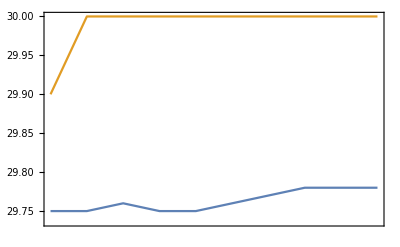

```mathematica
(*Chart the weather station's Pressure*)
pressure=data[[1;;All,2,1,7,2]]//Normal;

myPressureTimeSeries=TimeSeries[Transpose[{times, MapAt[ToExpression,#,1]&/@pressure}]];
wmoPressureTimeSeries=TimeSeries[Transpose[{times, AirPressureData["KBED", times]}]];
DateListPlot[{myPressureTimeSeries,wmoPressureTimeSeries}]
```